```mathematica
(*Rotating a set of points by given angle a*)
rotation[points_,angle_]:=Module[{p=points,a=angle},Return[p.{{Cos[a],-Sin[a]},{Sin[a],Cos[a]}}]]
(*Reflection of a se of points in symmetry of given axis*)
reflection[points_, axis_] := Module[{p = points, ax = axis},
If[ax == "X",Return[p.{{1,0},{0,-1}}],If[ax == "Y",Return[p.{{-1,0},{0,1}}],Return[p]]]]
```

```mathematica
(*Moving a set of points by given vector*)
translation[points_, vector_] := Module[{p = points, v = vector, l = Length[points]},
For[i = 1, i ≤ l, i++, p[[i,1]] = p[[i, 1]] + v[[1]]; p[[i,2]] = p[[i,2]] + v[[2]]];
Return[p]]
```

```mathematica
(*Resize set of points by given scale*)
```

```mathematica
scaling[points_, scale_] := Module[{p = points, n = scale, l = Length[points]},
If[n > 0,For[i = 1, i ≤ l, i++, p[[i,1]] = p[[i, 1]] * n; p[[i,2]] = p[[i,2]] * n]];
Return[p]]
```

```mathematica
(*EXAMPLES*)
```

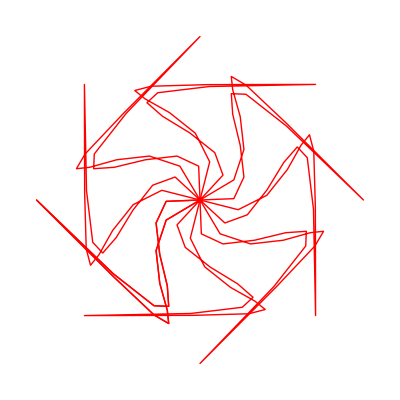

```mathematica
points={{0,0},{4,1},{-3,8},{5,0},{-3,8},{4,-1},{0,0}};
Graphics[{Red,BezierCurve[points],BezierCurve[rotation[points,Pi/2]],BezierCurve[rotation[points,-Pi/2]],BezierCurve[rotation[points,Pi/4]],BezierCurve[rotation[points,-Pi/4]],BezierCurve[rotation[points,3Pi/4]],BezierCurve[rotation[points,-3Pi/4]],BezierCurve[rotation[points,Pi]],BezierCurve[rotation[points,-Pi]]}]
```

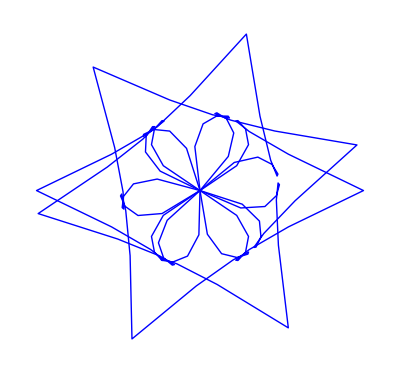

```mathematica
points1={{0,0},{6,3},{-4,5},{7,0},{-4,-5},{6,-3},{0,0}};
Graphics[{Blue, BezierCurve[points1],BezierCurve[rotation[points1, 1]],BezierCurve[rotation[points1, 2]], BezierCurve[rotation[points1, 3]], BezierCurve[rotation[points1, 4]],BezierCurve[rotation[points1, 5]],BezierCurve[rotation[points1, 6]],BezierCurve[reflection[points1,"Y"]]}]
```

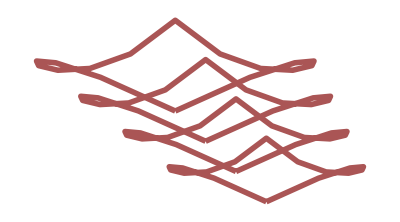

```mathematica
points2={{0,0},{-8,4},{-4,-1},{0,3},{4,-1},{8,4},{0,0}};
Graphics[{Darker[Pink],Thickness[0.01], BezierCurve[points2],BezierCurve[translation[scaling[points2, 0.9], {1,-1}]], BezierCurve[translation[scaling[points2, 0.8], {02,-2}]],BezierCurve[translation[scaling[points2, 0.7], {3,-3}]]}]
```